```mathematica
(* ФН2-72Б *)
(* Вариант 15 *)
SP[val_]:=SetPrecision[val,5];
eps=10^-10;
f[n_,ξ_]:=Piecewise[{{ξ^n/(n!), ξ>0}, {0, ξ≤0}}];
MyPlot[f_,a_,b_,arg_,y_]:=Plot[f, {x,a,b},AxesLabel->{Style[arg,Black,16, FontFamily->"Times"],Style[y,Black,16, FontFamily->"Times"]},LabelStyle->Directive[Black,14, FontFamily->"Times"],PlotStyle->{Purple,Thickness[0.004]},ImageSize->500,PlotRange->All];
MyPlotEpur[f_,a_,b_,arg_,y_,n_]:=
Show[MyPlot[f,a,b,arg,y],Graphics[{Lighter@Orange,Thickness[0.003],Line[{{1+eps,0.0},{1+eps,f/.{x->1+eps}}}],Line[{{2+eps,0.0},{2+eps,f/.{x->2+eps}}}]}~Join~Table[Line[{{a+(b-a)/(3n)*i,0.0},{a+(b-a)/(3n)*i,f/.{x->a+(b-a)/(3n)*i}}}],{i,1,3n}]~Join~{Opacity[1]}],MyPlot[f,a,b,arg,y]];
```

Задание 3

P3 = -M0/(2 L)+M1/(2 L)-P2/2+R0/2

P1 = M0/(2 L)-M1/(2 L)-P2/2+2 L q0-(3 R0)/2

Задание 4

P3 = R0/2

P1 = -(3 R0)/2

M3(x1) = R0 f1[x1]+P1 f1[-L+x1]

Q3(x1) = R0 f0[x1]+P1 f0[-L+x1]

M3(x1) = R0 f1[x1]-3/2 R0 f1[-L+x1]

Q3(x1) = R0 f0[x1]-3/2 R0 f0[-L+x1]

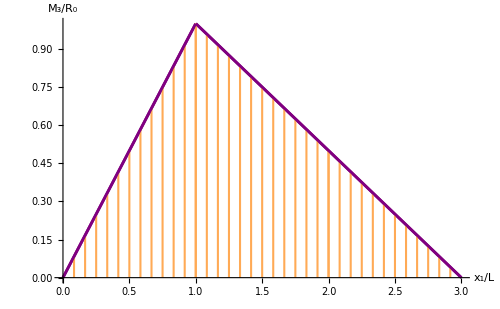

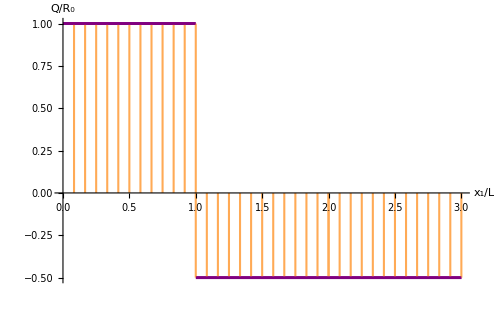

Задание 5

w(x1) = w01+w011 x1+(R0 f3[x1]-3/2 R0 f3[-L+x1])/(EE J3)

w01 = (L^3 (-7 ⅈ EE J3 Im[R0]+ⅈ R0 Im[J3] Re[EE]-R0 Im[EE] (Im[J3]-ⅈ Re[J3])+R0 Re[EE] Re[J3]-7 EE J3 Re[R0]))/(6 EE J3 (Im[EE]-ⅈ Re[EE]) (Im[J3]-ⅈ Re[J3])), w011 = (7 L^2 (ⅈ Im[R0]+Re[R0]))/(6 (Im[EE]-ⅈ Re[EE]) (Im[J3]-ⅈ Re[J3]))

w(x1) = ((3 R0 (2 f3[x1]-3 f3[-L+x1]) (Im[EE]-ⅈ Re[EE]) (Im[J3]-ⅈ Re[J3])+7 EE J3 L^2 x1 (ⅈ Im[R0]+Re[R0])+L^3 (-7 ⅈ EE J3 Im[R0]+ⅈ R0 Im[J3] Re[EE]-R0 Im[EE] (Im[J3]-ⅈ Re[J3])+R0 Re[EE] Re[J3]-7 EE J3 Re[R0]))/(6 EE J3 (Im[EE]-ⅈ Re[EE]) (Im[J3]-ⅈ Re[J3])))

wR0 = (L^3 (-7 ⅈ EE J3 Im[R0]+ⅈ R0 Im[J3] Re[EE]-R0 Im[EE] (Im[J3]-ⅈ Re[J3])+R0 Re[EE] Re[J3]-7 EE J3 Re[R0]))/(6 EE J3 (Im[EE]-ⅈ Re[EE]) (Im[J3]-ⅈ Re[J3]))

Задание 6

P3 = -(M0-M1+L P2)/(2 L)

P1 = (M0-M1-L P2+4 L^2 q0)/(2 L)

M3(x1) = -M0 f0[ξ]+M1 f0[-L+ξ]+P2 f1[-2 L+ξ]+P1 f1[-L+ξ]-q0 f2[ξ]+q0 f2[-2 L+ξ]

Q3(x1) = P2 f0[-2 L+ξ]+P1 f0[-L+ξ]-q0 f1[ξ]+q0 f2[-2 L+ξ]

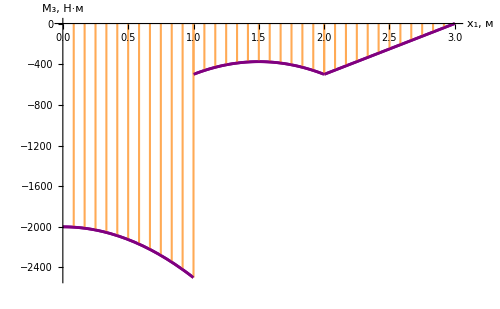

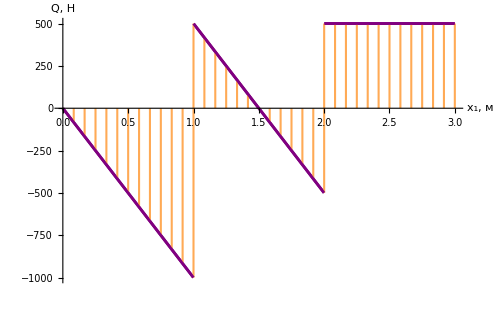

Задание 7

w(x1) = w02+w022 x1+(-M0 f2[ξ]+M1 f2[-L+ξ]+P2 f3[-2 L+ξ]+P1 f3[-L+ξ]-q0 f4[ξ]+q0 f4[-2 L+ξ])/(EE J3)

w02 = ((L^2 (80 ⅈ EE J3 Im[M0]-32 ⅈ EE J3 Im[M1]+12 ⅈ EE J3 L Im[P2]+15 ⅈ EE J3 L^2 Im[q0]-24 ⅈ M0 Im[J3] Re[EE]-2 ⅈ L^2 q0 Im[J3] Re[EE]+2 (12 M0+L^2 q0) Im[EE] (Im[J3]-ⅈ Re[J3])-24 M0 Re[EE] Re[J3]-2 L^2 q0 Re[EE] Re[J3]+80 EE J3 Re[M0]-32 EE J3 Re[M1]+12 EE J3 L Re[P2]+15 EE J3 L^2 Re[q0]))/(48 EE J3 (Im[EE]-ⅈ Re[EE]) (Im[J3]-ⅈ Re[J3]))), w022 = (L (-80 ⅈ Im[M0]+32 ⅈ Im[M1]-12 ⅈ L Im[P2]-15 ⅈ L^2 Im[q0]-80 Re[M0]+32 Re[M1]-12 L Re[P2]-15 L^2 Re[q0]))/(48 (Im[EE]-ⅈ Re[EE]) (Im[J3]-ⅈ Re[J3]))

w(x1) = ((-24 (2 L M0 f2[ξ]-2 L M1 f2[-L+ξ]-2 L P2 f3[-2 L+ξ]-(M0-M1+L (-P2+4 L q0)) f3[-L+ξ]+2 L q0 f4[ξ]-2 L q0 f4[-2 L+ξ]) (Im[EE]-ⅈ Re[EE]) (Im[J3]-ⅈ Re[J3])-EE J3 L^2 x1 (80 ⅈ Im[M0]-32 ⅈ Im[M1]+12 ⅈ L Im[P2]+15 ⅈ L^2 Im[q0]+80 Re[M0]-32 Re[M1]+12 L Re[P2]+15 L^2 Re[q0])+L^3 (80 ⅈ EE J3 Im[M0]-32 ⅈ EE J3 Im[M1]+12 ⅈ EE J3 L Im[P2]+15 ⅈ EE J3 L^2 Im[q0]-24 ⅈ M0 Im[J3] Re[EE]-2 ⅈ L^2 q0 Im[J3] Re[EE]+2 (12 M0+L^2 q0) Im[EE] (Im[J3]-ⅈ Re[J3])-24 M0 Re[EE] Re[J3]-2 L^2 q0 Re[EE] Re[J3]+80 EE J3 Re[M0]-32 EE J3 Re[M1]+12 EE J3 L Re[P2]+15 EE J3 L^2 Re[q0]))/(48 EE J3 L (Im[EE]-ⅈ Re[EE]) (Im[J3]-ⅈ Re[J3])))

w0 = ((L^2 (80 ⅈ EE J3 Im[M0]-32 ⅈ EE J3 Im[M1]+12 ⅈ EE J3 L Im[P2]+15 ⅈ EE J3 L^2 Im[q0]-24 ⅈ M0 Im[J3] Re[EE]-2 ⅈ L^2 q0 Im[J3] Re[EE]+2 (12 M0+L^2 q0) Im[EE] (Im[J3]-ⅈ Re[J3])-24 M0 Re[EE] Re[J3]-2 L^2 q0 Re[EE] Re[J3]+80 EE J3 Re[M0]-32 EE J3 Re[M1]+12 EE J3 L Re[P2]+15 EE J3 L^2 Re[q0]))/(48 EE J3 (Im[EE]-ⅈ Re[EE]) (Im[J3]-ⅈ Re[J3])))

Задание 8

R0 = (7 ⅈ Im[M0])/(6 L)-(2 ⅈ Im[M1])/(3 L)+1/4 ⅈ Im[P2]+13/48 ⅈ L Im[q0]+(7 Re[M0])/(6 L)-(2 Re[M1])/(3 L)+Re[P2]/4+13/48 L Re[q0]

P3 = -M0/(2 L)+M1/(2 L)-P2/2+(7 ⅈ Im[M0])/(12 L)-(ⅈ Im[M1])/(3 L)+1/8 ⅈ Im[P2]+13/96 ⅈ L Im[q0]+(7 Re[M0])/(12 L)-Re[M1]/(3 L)+Re[P2]/8+13/96 L Re[q0]

P1 = M0/(2 L)-M1/(2 L)-P2/2+2 L q0-(7 ⅈ Im[M0])/(4 L)+(ⅈ Im[M1])/L-3/8 ⅈ Im[P2]-13/32 ⅈ L Im[q0]-(7 Re[M0])/(4 L)+Re[M1]/L-(3 Re[P2])/8-13/32 L Re[q0]

R0 = 1520.8 H

P3 = 260.42 H

P1 = -781.25 H

Задание 9.1

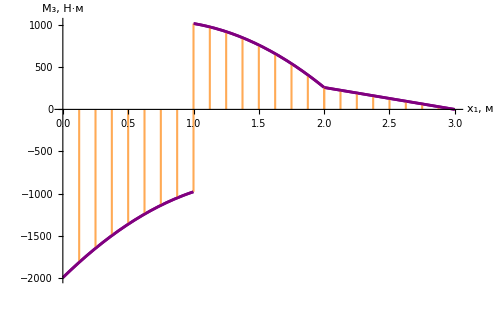

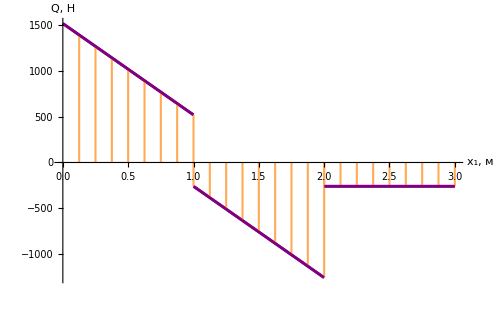

Задание 9.2

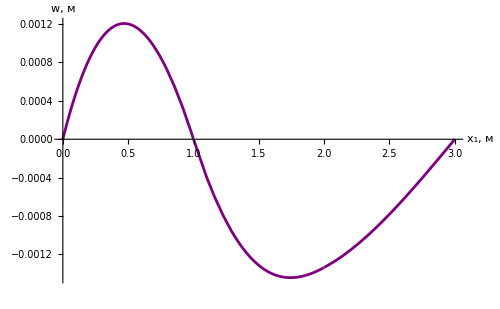

Задание 10

σmax = 94.675 МПа

```mathematica
(* Параметры *)
M=2000;
P=1000;
pq0=1000;
pL=1;
b=3/100;
h=65/1000;
pE=210*10^9;
prm={M0->M,M1->M,P2->P,q0->pq0,L->pL,b->pb,h->ph,EE->pE,J3->(b*h^3)/12};
Print["Задание 3"];
sol3=Solve[{R0+P1+P2+P3-2L*q0==0,M0+L*P1+2L*P2-M1+3L*P3-2 L^2*q0==0},{P3,P1}]⟦1⟧//Simplify;
Print["P3 = ",P3/.sol3//Expand];
Print["P1 = ",P1/.sol3//Expand];
Print["Задание 4"];
sol41=Solve[{R0+P1+P3==0,L*P1+3L*P3==0},{P3,P1}]⟦1⟧//Simplify;
Print["P3 = ",P3/.sol41];
Print["P1 = ",P1/.sol41];
M31[ξ_]:=R0*f[1,ξ]+P1*f[1,ξ-L]/.sol41//Simplify;
Q31[ξ_]:=M31'[ξ]//Simplify;
Print["M3(x1) = ",R0*f1[x1]+P1*f1[x1-L]];
Print["Q3(x1) = ",R0*f0[x1]+P1*f0[x1-L]];
Print["M3(x1) = ",R0*f1[x1]+P1*f1[x1-L]/.sol41//Simplify];
Print["Q3(x1) = ",R0*f0[x1]+P1*f0[x1-L]/.sol41//Simplify];
Print@MyPlotEpur[(M31[x]/.{R0->1}/.prm),0,3,"x_1/L","M_3/R_0",12];
Print@MyPlotEpur[(Q31[x]/.{R0->1}/.prm),0,3,"x_1/L","Q/R_0",12];
Print["Задание 5"];
Print["w(x1) = ",w01+w011*x1+1/(EE*J3)(R0*f3[x1]+P1*f3[x1-L])/.sol41//Simplify];
w1[ξ_]:=w01+w011*ξ+1/(EE*J3)(R0*f[3,ξ]+P1*f[3,ξ-L]/.sol41)//Simplify;
solw01=Assuming[L>0,Solve[{w1[L]==0,w1[3L]==0},{w01,w011}]]⟦1⟧//Simplify;
Print["w01 = ",w01/.solw01,", w011 = ",w011/.solw01];
Print["w(x1) = ",w01+w011*x1+1/(EE*J3)(R0*f3[x1]+P1*f3[x1-L])/.sol41/.solw01//Simplify];
w1[ξ_]:=w01+w011*ξ+1/(EE*J3)(R0*f[3,ξ]+P1*f[3,ξ-L])/.sol41/.solw01//Simplify;
wR0=Assuming[L>0,w1[0]];
Print["wR0 = ", wR0];
Print["Задание 6"];
sol61=Solve[{P3+P1+P2-2L*q0==0,M0+L*P1+2L*P2-M1+3L*P3-2 L^2*q0==0},{P3,P1}]⟦1⟧//Simplify;
Print["P3 = ",P3/.sol61];
Print["P1 = ",P1/.sol61];
M32[ξ_]:=M1*f[0,ξ-L]-M0*f[0,ξ]+P1*f[1,ξ-L]+P2*f[1,ξ-2L]-q0*f[2,ξ]+q0*f[2,ξ-2L]/.sol61//Simplify;
Q32[ξ_]:=M32'[ξ]//Simplify;
Print["M3(x1) = ",M1*f0[ξ-L]-M0*f0[ξ]+P1*f1[ξ-L]+P2*f1[ξ-2L]-q0*f2[ξ]+q0*f2[ξ-2L]];
Print["Q3(x1) = ",P1*f0[ξ-L]+P2*f0[ξ-2L]-q0*f1[ξ]+q0*f2[ξ-2L]];
Print@MyPlotEpur[(M32[x]/.prm),0,3,"x_1, м","M_3, Н·м",12];
Print@MyPlotEpur[(Q32[x]/.prm),0,3,"x_1, м","Q, Н",12];
Print["Задание 7"];
Print["w(x1) = ",w02+w022*x1+1/(EE*J3)(M1*f2[ξ-L]-M0*f2[ξ]+P1*f3[ξ-L]+P2*f3[ξ-2L]-q0*f4[ξ]+q0*f4[ξ-2L])];
w2[ξ_]:=w02+w022*ξ+1/(EE*J3)(M1*f[2,ξ-L]-M0*f[2,ξ]+P1*f[3,ξ-L]+P2*f[3,ξ-2L]-q0*f[4,ξ]+q0*f[4,ξ-2L])/.sol61//Simplify;
solw02=Assuming[L>0,Solve[{w2[L]==0,w2[3L]==0},{w02,w022}]]⟦1⟧//Simplify;
Print["w02 = ",(w02/.solw02//Simplify),", w022 = ",(w022/.solw02//Simplify)];
Print["w(x1) = ",w02+w022*x1+1/(EE*J3)(M1*f2[ξ-L]-M0*f2[ξ]+P1*f3[ξ-L]+P2*f3[ξ-2L]-q0*f4[ξ]+q0*f4[ξ-2L])/.sol61/.solw02//Simplify];
w2[ξ_]:=w02+w022*ξ+1/(EE*J3)(M1*f[2,ξ-L]-M0*f[2,ξ]+P1*f[3,ξ-L]+P2*f[3,ξ-2L]-q0*f[4,ξ]+q0*f[4,ξ-2L])/.sol61/.solw02//Simplify;
wNOR=Assuming[L>0,w2[0]];
Print["w0 = ", wNOR];
Print["Задание 8"];
sol8=Assuming[L>0,Solve[wR0+wNOR==0,R0]]⟦1⟧//Simplify;
Print["R0 = ",R0/.sol8//Expand];
Print["P3 = ",P3/.sol3/.sol8//Expand];
Print["P1 = ",P1/.sol3/.sol8//Expand];
Print["R0 = ", SP[R0/.sol8/.prm]," H"];
Print["P3 = ", SP[P3/.sol3/.sol8/.prm]," H"];
Print["P1 = ", SP[P1/.sol3/.sol8/.prm]," H"];
Print["Задание 9.1"];
Mexpr=(M31[x]+M32[x])/.sol8/.prm//FullSimplify;
Qexpr=(Q31[x]+Q32[x])/.sol8/.prm//FullSimplify;
Print@MyPlotEpur[Mexpr,0,3,"x_1, м","M_3, Н·м",8];
Print@MyPlotEpur[Qexpr,0,3,"x_1, м","Q, Н",8];
Print["Задание 9.2"];
wExpr=(w1[x]+w2[x])/.sol8/.prm//FullSimplify;
Print@MyPlot[wExpr,0,3,"x_1, м","w, м"];
Print["Задание 10"];
Mmax=M0;
W3=(b*h^2)/6;
σmax=Mmax/W3;
Print["σmax = ", SP[σmax*10^-6/.prm]," МПа"];
```